```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
NS["study_pairgenes"]
```

```mathematica
res=Import["results_pairs2.csv"];
```

```mathematica
Dimensions[res]
```

{4371,3}

```mathematica
{Min@res[[;;,3]],Max@res[[;;,3]]}
```

{0.00009995,0.00428197}

```mathematica
Log[10,%]
```

{-4.00022,-2.36836}

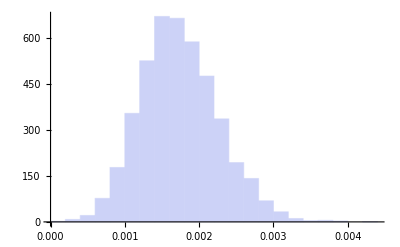

```mathematica
Histogram[res[[;;,3]],"Knuth",PlotRange->All]
```

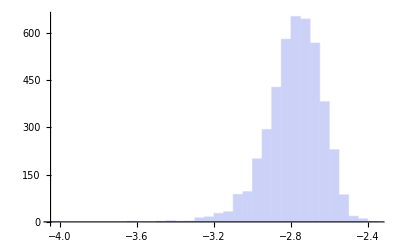

```mathematica
Histogram[Log[10,res[[;;,3]]],"Knuth",PlotRange->All]
```

```mathematica
sortres=Sort[res,#1[[3]]>#2[[3]]&];
```

```mathematica
sortres[[1;;20,;;]]//MF
```

(68 | 89 | 0.00428197
88 | 89 | 0.00392101
59 | 90 | 0.00391304
32 | 89 | 0.00383417
59 | 89 | 0.00378546
89 | 90 | 0.00376354
64 | 89 | 0.0037567
72 | 89 | 0.00361801
6 | 57 | 0.00361688
61 | 88 | 0.00359064
69 | 89 | 0.00356539
9 | 58 | 0.00352329
32 | 66 | 0.00349298
34 | 89 | 0.00337852
46 | 90 | 0.00337457
31 | 66 | 0.00331328
6 | 53 | 0.0033014
6 | 21 | 0.00327939
42 | 68 | 0.00327784
9 | 38 | 0.00327634)

```mathematica
94*93/2
```

4371

```mathematica
tab=Table[Tally[Flatten@sortres[[1;;i,1;;2]]],{i,60}];
```

```mathematica
tab[[6]]
```

{{68,1},{89,5},{88,1},{59,2},{90,2},{32,1}}

```mathematica
tab2=Table[Union[Flatten@sortres[[1;;i,1;;2]]],{i,60}];
```

```mathematica
best={};i=1;While[Length@best<5,best=Union[Flatten@sortres[[1;;i,1;;2]]];i=i+1];
```

```mathematica
best
```

{59,68,88,89,90}

```mathematica
best2={};i=1;While[sortres[[i,3]]>0.003,best2=Union[Flatten@sortres[[1;;i,1;;2]]];i=i+1];Length@best2
```

45

```mathematica
best2
```

{3,6,9,16,17,20,21,26,30,31,32,33,34,35,38,42,46,51,52,53,55,57,58,59,61,64,66,67,68,69,70,72,75,77,78,79,82,83,85,88,89,90,91,92,93}